-4 x1^2+4 x0 (x0^2+x1^2)+(x0^2+x1^2)^2

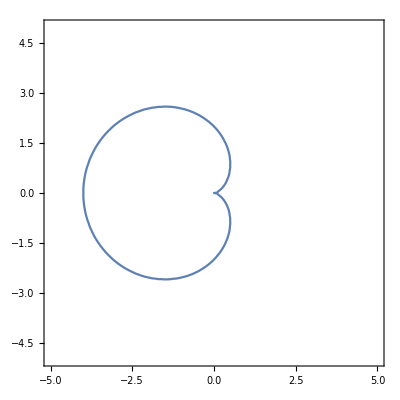

```mathematica
f = (x0^2 + x1^2)^2 + 4 x0 (x0^2 + x1^2) - 4 x1^2
ContourPlot[f==0,{x0,-5,5},{x1,-5,5}]
```

-4+12 u0+15 u0^2+4 u0^3+27 u1^2

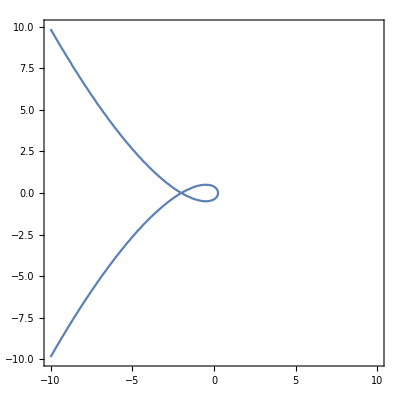

x0^4 + 2*x0^2*x1^2 + x1^4 + 4*x0^3*x2 + 4*x0*x1^2*x2 - 4*x1^2*x2^2

```mathematica
h = ResourceFunction["PolynomialHomogenize"][Expand[f],{x0, x1},x2];
h //InputForm

d = 4*u0^3+15*u0^2*u2+27*u1^2*u2+12*u0*u2^2-4*u2^3;
s = d /. u2-> 1
ContourPlot[s == 0, {u0, -10, 10}, {u1, -10, 10}]
```